```mathematica
randomDirection:=Module[{cosTheta,sinTheta,phi},
cosTheta=RandomReal[{-1,1}];
phi=RandomReal[2π];
sinTheta=√(1-cosTheta^2);
{cosTheta,sinTheta Sin[phi],sinTheta Cos[phi]}];
```

```mathematica
x3Gaussian:=√(-Log[RandomReal[]RandomReal[]]);
```

```mathematica
x2Gaussian:=√(1/2(RandomVariate[NormalDistribution[0,1]])^2-Log[RandomReal[]]);
```

```mathematica
getVpAndCosine[vpRms_,vn_]:=
Module[{β,y,x,μ,vp},
β=1/(√2 vpRms);
y=β vn;
While[True,
x=If[RandomReal[]<2/(√π y+2),x3Gaussian,x2Gaussian];
vp=x/β;
μ=RandomReal[{-1,1}];
If[RandomReal[]<(√(vn^2+vp^2-2vn vp μ))/(vn+vp),Break[]];
];
{vp,μ}
]
```

```mathematica
scatterE[erg0_]:=Module[{vecVn,vecVp,vecVcm,vecVnout,vn,vp,μ,mn=939.565,mp=938.272,kT=2.53*^-8},
vn=√(2 erg0/mn);
{vp,μ}=getVpAndCosine[√(kT/mp),vn];
vecVn=vn{1,0,0};
vecVp=vp{μ,√(1-μ^2),0};
vecVcm=-(mn vecVn+mp vecVp)/(mn+mp);
vecVnout=Norm[vecVn+vecVcm]randomDirection-vecVcm;
1/2 mn vecVnout.vecVnout];
```

```mathematica
hlist2=HistogramList[Table[scatterE[2.53*^-8],10000000],{1.0*^-9}];
```

```mathematica
factor = (1-Exp[-0.082572 0.025 csElasticH[2.53*^-8]])/(4π 20.5^2)
```

0.0000114008

```mathematica
csElasticH[2.53*^-8]
```

30.0812

```mathematica
data2=plotData[hlist2,factor];
```

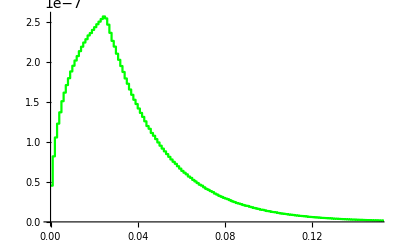

```mathematica
plot2=ListStepPlot[data2,PlotRange->{{0,0.15},All},PlotStyle->Green]
```